Script for generating data for linear regression through feedback control example.

```mathematica
SeedRandom[3210]; (*Use a radom seed for reproducibility*)

datasetSize =125; (*Total size of the dataset, training and test*)
testFraction = 0.2; (*Fraction of the total dataset used as test data*)
nEpochs = 7; (*Number of times the data is shown to the learner*)

testSize = Round[datasetSize*testFraction];
trainSize = datasetSize - testSize;


dataSampleRate = 100; (*Samples presented to the learner per second*)
pauseDuration = 1; (* Nothing happens for 2 sections between training and testing*)
totalSimulationDuration = datasetSize*nEpochs/dataSampleRate + pauseDuration //N(*Data is presented multiple times (epochs)*)

(*Linearly increasing timesteps for table required by SystemModeler*)
simulationTimestamps = Range[0,totalSimulationDuration-1/dataSampleRate,1/dataSampleRate];

(*x data is uniformly distributed betweeb 0 and 1*)
x = RandomReal[{0,1},datasetSize];

(*Parameters w1 and b1 are used to generate data. These are also the parameters that we hope to infer from the data during training*)
w1 = 0.9   (*One of the parameters we are trying to infer through feedback control*);
b1 = -0.1 (*The second parameter that will be inferred*);
y = #*w1 + b1 + RandomVariate[NormalDistribution[0,0.1]]  &/@x; (*Generate the data with some Gaussian noise. Notice standard deviation 0.1 *)

(*Randomly shuffle datapoints, then split into testing and training sets*)
permutation=RandomPermutation[datasetSize]; 

xPerm = Permute[x,permutation];
yPerm = Permute[y,permutation];

xTrain = Take[xPerm,trainSize];
xTest = Take[xPerm,-testSize];

yTrain = Take[yPerm,trainSize];
yTest = Take[yPerm,-testSize];

(*Define a function that repeats the training data for different epochs*)
repeatData[listtorepeat_,nrepeat_]:=Flatten@Table[listtorepeat,nrepeat]

(*Stack the data. The simulation will have three phases: training, pause, Test/evaluation)*)
pause = ConstantArray[0,Round[pauseDuration*dataSampleRate]];(*During pause, x=0,y=0*)
xAll = Join[
repeatData[xTrain,nEpochs], pause,repeatData[xTest,nEpochs]
];
yAll = Join[
repeatData[yTrain,nEpochs], pause,repeatData[yTest,nEpochs]
];

(*Assign each datapoint to a time step as required by SystemModeler*)
xDat = Transpose@{simulationTimestamps,xAll};
yDat = Transpose@{simulationTimestamps,yAll};

(*Export in Matlab format that can be read by Modelica block*)
Export["/home/douwm/projects/side_projects/analogue_logistic_regression/data.mat",{"x"->xDat,"y"->yDat}]
```

9.75

/home/douwm/projects/side_projects/analogue_logistic_regression/data.mat

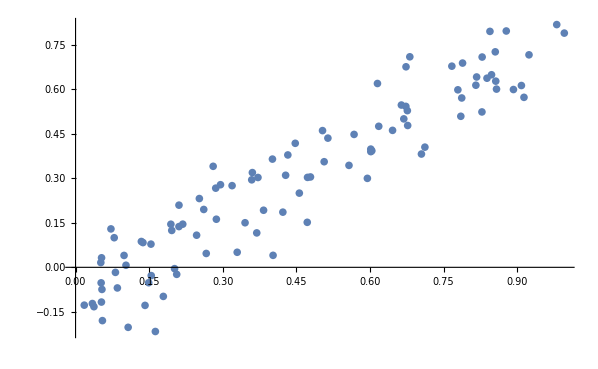

```mathematica
ListPlot[Transpose[{xTrain,yTrain}]] (*We will fit the model y = w1*x + b1 to this data using feedback control*)
```

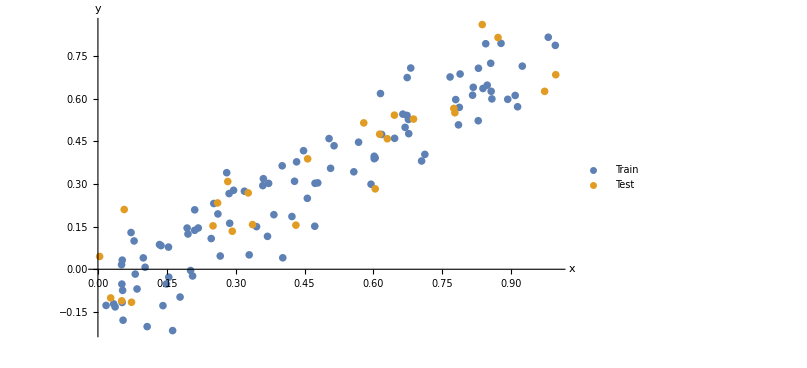

```mathematica
ListPlot[{Transpose[{xTrain,yTrain}],Transpose[{xTest,yTest}]},AxesLabel->{HoldForm[x],HoldForm[y]},PlotLegends->{"Train","Test"}]
```

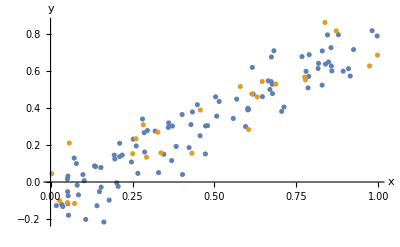

```mathematica
Show[%52,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLegends->{"A","B"}]
```

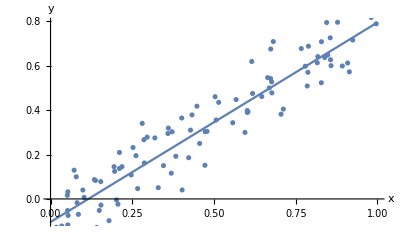

Fitted model: y = -0.103933+0.89864 w

Standard deviation of errors: 0.0962986

```mathematica
data=Transpose[{xTrain,yTrain}];

lmf=LinearModelFit[data,w,w];
Show[Plot[lmf[x],{x,0,1}],ListPlot[data],AxesLabel->{HoldForm[x],HoldForm[y]}]

Print["Fitted model: y = ",Normal[lmf]];
Print["Standard deviation of errors: ",Sqrt[lmf["EstimatedVariance"]]];
```

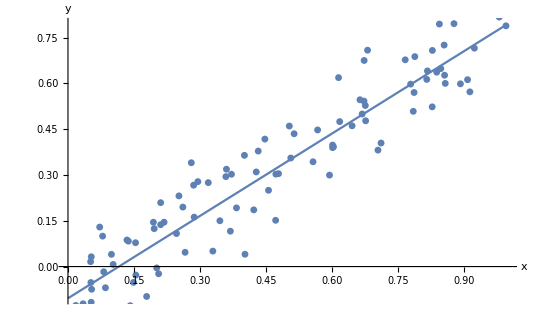

-Graphics-

```mathematica
xTrain
```

{0.319048,0.0342842,0.924232,0.201807,0.107206,0.162678,0.149103,0.681301,0.0374714,0.153691,0.447798,0.980771,0.67695,0.286986,0.210798,0.601798,0.838611,0.137404,0.42253,0.371797,0.0537839,0.785248,0.0812643,0.594806,0.603872,0.369319,0.673232,0.815939,0.428189,0.669039,0.472809,0.456103,0.196075,0.359102,0.401303,0.252337,0.617969,0.514326,0.996194,0.908761,0.787128,0.712043,0.855498,0.856473,0.402577,0.246734,0.664098,0.178902,0.788826,0.154283,0.098844,0.877902,0.0527427,0.766984,0.0529968,0.472261,0.506727,0.280472,0.194275,0.329465,0.210739,0.817496,0.50339,0.261293,0.0787771,0.052142,0.0852279,0.828306,0.206172,0.134116,0.828731,0.266379,0.892529,0.141622,0.673552,0.0177511,0.601757,0.847858,0.478811,0.285693,0.913999,0.383217,0.0721228,0.64613,0.0547447,0.615354,0.858026,0.567687,0.102781,0.84464,0.34549,0.295422,0.360393,0.704991,0.218519,0.676275,0.779258,0.0514843,0.432684,0.557319}